https://www.cockcroft.ac.uk/wp-content/uploads/2018/04/LWFA_comp.pdf

## Plasma wave generation by a laser pulse

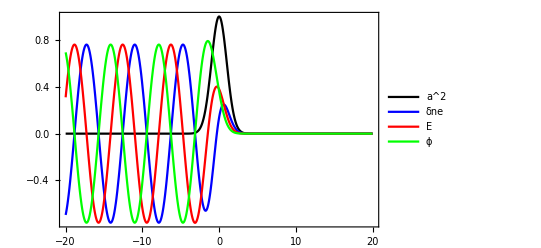

```mathematica
(* clear variables *)
Clear[a,kp,σξ,ξ,Ex,ϕ, eps, pltpnt,asp,imgsz]

(** plot style **)
(* contour precision *)
eps=0.0001;
(* point density *)
pltpnt=60;
(* aspect ratio *)
asp = 0.62;
(* image size *)
imgsz=400;

(* normalizing wavevector *)
kp=1;

(* laser function *)
a[ξ_]:=Exp[-0.5ξ^2/σξ^2]
(* width *)
σξ= √2;

(* plot laser *)
plt1=Plot[a[ξ]^2,{ξ,-20,+20},PlotStyle->Black,Axes->False,Frame->True,PlotRange->All,PlotLegends->{"a^2"},AspectRatio->asp,ImageSize->imgsz];

(* to get electron density perturbation, solve differential equation *)
solδne=NDSolve[{D[δne[ξ],{ξ,2}]+kp^2 δne[ξ]==1/2 D[a[ξ]^2,{ξ,2}],δne[20]==0,δne'[20]==0},δne[ξ],{ξ,-20,+20}];
plt2=Plot[Evaluate[δne[ξ]/.solδne],{ξ,-20,20},PlotStyle->Blue,Axes->False,Frame->True,PlotLegends->{"δne"},AspectRatio->asp,ImageSize->imgsz];

(* to get field, integrate density *)
solEx=NDSolve[{D[Ex[ξ],ξ]==-δne[ξ]/.solδne,Ex[20]==0},Ex[ξ],{ξ,-20,+20}];
plt3=Plot[Evaluate[Ex[ξ]/.solEx],{ξ,-20,20},PlotStyle->Red,Axes->False,Frame->True,PlotLegends->{"E"},AspectRatio->asp,ImageSize->imgsz];

(* to get potential, integrate field *)
solϕ=NDSolve[{D[ϕ[ξ],ξ]==-Ex[ξ]/.solEx,ϕ[20]==0},ϕ[ξ],{ξ,-20,+20}];
plt4=Plot[Evaluate[ϕ[ξ]/.solϕ],{ξ,-20,20},PlotStyle->Green,Axes->False,Frame->True,PlotLegends->{"ϕ"},AspectRatio->asp,ImageSize->imgsz];

(* overlay all plots *)
Show[{plt1,plt2,plt3,plt4},PlotRange->All,PlotLegends->Automatic]
```

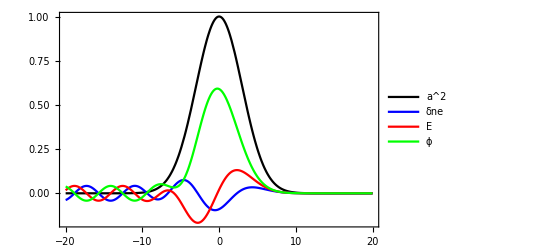

```mathematica
(* clear variables *)
Clear[a,kp,σξ,ξ,Ex,ϕ, eps, pltpnt,asp,imgsz]

(** plot style **)
(* contour precision *)
eps=0.0001;
(* point density *)
pltpnt=60;
(* aspect ratio *)
asp = 0.62;
(* image size *)
imgsz=400;

(* normalizing wavevector *)
kp=1;

(* laser function *)
a[ξ_]:=Exp[-0.5ξ^2/σξ^2]
(* width *)
σξ=3 √2;

(* plot laser *)
plt1=Plot[a[ξ]^2,{ξ,-20,+20},PlotStyle->Black,Axes->False,Frame->True,PlotRange->All,PlotLegends->{"a^2"},AspectRatio->asp,ImageSize->imgsz];

(* to get electron density perturbation, solve differential equation *)
solδne=NDSolve[{D[δne[ξ],{ξ,2}]+kp^2 δne[ξ]==1/2 D[a[ξ]^2,{ξ,2}],δne[20]==0,δne'[20]==0},δne[ξ],{ξ,-20,+20}];
plt2=Plot[Evaluate[δne[ξ]/.solδne],{ξ,-20,20},PlotStyle->Blue,Axes->False,Frame->True,PlotLegends->{"δne"},AspectRatio->asp,ImageSize->imgsz];

(* to get field, integrate density *)
solEx=NDSolve[{D[Ex[ξ],ξ]==-δne[ξ]/.solδne,Ex[20]==0},Ex[ξ],{ξ,-20,+20}];
plt3=Plot[Evaluate[Ex[ξ]/.solEx],{ξ,-20,20},PlotStyle->Red,Axes->False,Frame->True,PlotLegends->{"E"},AspectRatio->asp,ImageSize->imgsz];

(* to get potential, integrate field *)
solϕ=NDSolve[{D[ϕ[ξ],ξ]==-Ex[ξ]/.solEx,ϕ[20]==0},ϕ[ξ],{ξ,-20,+20}];
plt4=Plot[Evaluate[ϕ[ξ]/.solϕ],{ξ,-20,20},PlotStyle->Green,Axes->False,Frame->True,PlotLegends->{"ϕ"},AspectRatio->asp,ImageSize->imgsz];

(* overlay all plots *)
Show[{plt1,plt2,plt3,plt4},PlotRange->All,PlotLegends->Automatic]
```

## Particle trapping in 1D plasma wave: Phase-space trajectories

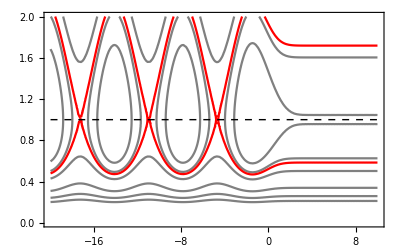

```mathematica
(* we now move on to phase-space trajectories *)

(* wave gamma *)
γϕ=10;βϕ=Sqrt[1-1/γϕ^2];
(* initial momentum *)
γ0={10,16,20,30,40,50};β0=Sqrt[1-1/γ0^2];

(* scan different initial momenta to get trajectories in phase-space *)
plt={};
For[i=1,i≤Length[γ0],i++,
AppendTo[plt,ContourPlot[(γ γϕ-βϕ Sqrt[(γ γϕ)^2-1]-1/50ϕ[ξ]/.solϕ)==eps+(γ0[[i]]-βϕ Sqrt[γ0[[i]]^2-1]),{ξ,-20,+10},{γ,0,2},ContourStyle->Gray,AspectRatio->asp,PlotPoints->pltpnt,ImageSize->imgsz]]
];

(* this value is close to separatrix *)
γ0=17.15;
AppendTo[plt,ContourPlot[(γ γϕ-βϕ Sqrt[(γ γϕ)^2-1]-1/50ϕ[ξ]/.solϕ)==eps+(γ0-βϕ Sqrt[γ0^2-1]),{ξ,-20,+10},{γ,0,2},ContourStyle->Red,AspectRatio->asp,PlotPoints->pltpnt,ImageSize->imgsz]];

(* symmetry line *)
line=Graphics[{Dashed,Black,Line[{{-20,1},{10,1}}]}];

(* overlay plots *)
Show[{plt,line}]
```